```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 11:01:05
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

## BoudaryCell-Example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
w=RandomizeTemplate[TemplateRectangular[{0,10,2}, {0,10,2}], .1];
```

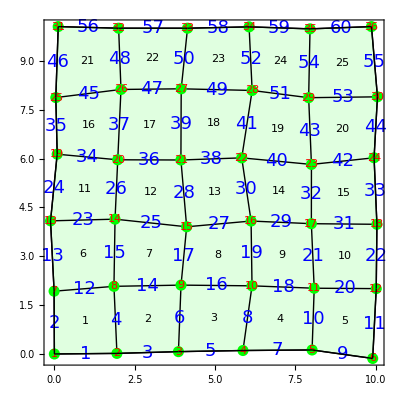

```mathematica
ShowTissue[w, Frame-> True, "Vertices"-> {Directive[Green,PointSize[.02]]},"VertexNumbers"-> {Directive[Red, FontSize-> 18]}, 
"EdgeNumbers"-> True, 
"EdgeNumberStyle"-> Directive[Blue, FontSize-> 18, FontFamily-> "Arial"],  "CellNumbers"-> True]
```

```mathematica
bcw=BoundaryCell[w]
```

{Coordinates→{{-0.00328137,0.00582399},{1.94523,0.023244},{3.86068,0.0770106},{5.87053,0.111882},{8.02325,0.128301},{9.91093,-0.131692},{10.0211,2.01043},{10.0423,3.9837},{9.95393,6.02446},{10.0593,7.89423},{9.87368,10.0487},{7.95886,9.97957},{6.06147,10.0408},{4.14393,9.99921},{1.99792,9.99979},{0.116888,10.0492},{0.0418504,7.87111},{0.0843164,6.13414},{-0.122623,4.08916},{-0.0114708,1.93162}},Edges→{1,3,5,7,9,11,22,33,44,55,60,59,58,57,56,46,35,24,13,2},Vertices→{1,2,3,4,5,6,12,18,24,30,36,35,34,33,32,31,25,19,13,7}}

### Create a new tissue from the edges of the original tissue

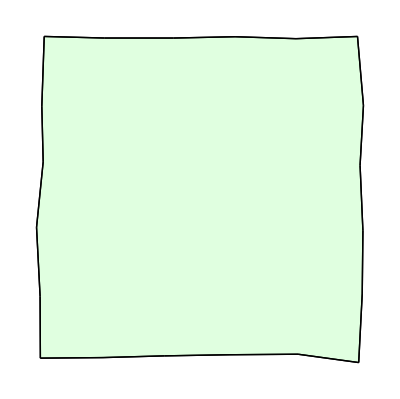

```mathematica
c="Edges"/.bcw;
v=TissueVertices[w];
e=TissueEdges[w];
T=Tissue[v,e,{c}];
ShowTissue[T]
```